```mathematica
Lecture 12: Number Theory
```

## Divisors

### Exercise Subsection

Show that n^2 must have remainder 0, 1, or 4 modulo 5 (at least for the values of n up to 10^6).

```mathematica
DeleteDuplicates@Mod[Range[10^6]^2,5]
```

{1,4,0}

### Exercise Subsection

Show that the number 1111...1 (every digit of the integer is 1) must have remainder 3 modulo 4 (at least for the first 1000 integers of this form).

```mathematica
number[n_]:=FromDigits[Table[1,n]]
```

```mathematica
Rest@Mod[number/@Range@1000,4]//DeleteDuplicates
```

{3}

### Exercise Subsection

Use ExtendedGCD to find integers x and y such that (2^100-1) x + (3^100-1) y == GCD[2^100-1, 3^100-1].

```mathematica
?ExtendedGCD
```

```mathematica
ExtendedGCD[2^100-1,3^100-1]
```

{138875,{-1162697940518182615500677620742689502959163,2859835136170798900894420}}

```mathematica
-1162697940518182615500677620742689502959163 (2^100-1)+2859835136170798900894420 (3^100 -1)
```

138875

## Primes

### Exercise Subsection

Find a counterexample to the conjecture that if a positive integer n larger than 2 divides 2^n−2, then n is prime .

```mathematica
Cases[Range@1000,n_/;Mod[2^n-2,n]==0&&Not@PrimeQ@n]
```

{1,341,561,645}

### Exercise Subsection

Let a, b, and c be the integers defined in the next cell.  Show that b and c are prime and that a is the product of b and c. 

While this exercise may not be difficult, it has historical significance.  The belief that nobody can factor integers quickly is the basis for some commonly used modern cryptographic systems.  From 1991 through 2007, the network security company RSA awarded prizes to anyone who could factor one of the integers on a list of challenge numbers.  The last challenge number that has been factored is the a below, which took over 3 years of computing time in 2009 (the command FactorInteger@a will probably take many years to run on your laptop!)

```mathematica
{a,b,c}={1230186684530117755130494958384962720772853569595334792197322452151726400507263657518745202199786469389956474942774063845925192557326303453731548268507917026122142913461670429214311602221240479274737794080665351419597459856902143413,33478071698956898786044169848212690817704794983713768568912431388982883793878002287614711652531743087737814467999489,36746043666799590428244633799627952632279158164343087642676032283815739666511279233373417143396810270092798736308917};
```

```mathematica
{a==b c,PrimeQ@b,PrimeQ@c}
```

{True,True,True}

### Exercise Subsection

The Riemann hypothesis is probably the most notorious unsolved problem in mathematics.  It is related to the distribution of primes.  There are many equivalent statements to the Riemann hypothesis, one says that the inequality in the next cell holds for values of n larger than 2657:

```mathematica
Abs[-NIntegrate[1/Log[t],{t,2,n}]+PrimePi[n]]≤(√n Log[n])/(8 π)
```

Show that the above inequality is true for all integers n larger than 3000 and less than 5000. 

Note: If you randomly select a large enough n and the above test happens to be False, then you have resolved the Riemann hypothesis in the negative and will earn a $1,000,000 prize.

### Exercise Subsection

An open problem is to prove that there is always a prime between n^2 and (n+1)^2 for integers n larger than 2.  Verify this conjecture is true as the integer n ranges from 2 to 10^4.

```mathematica
Table[Count[Range[n^2,(n+1)^2],x_/;PrimeQ@x],{n,10^4}]
```

{2,2,2,3,2,4,3,4,3,5,4,5,5,4,6,7,5,6,6,7,7,7,6,9,8,7,8,9,8,8,10,9,10,9,10,9,9,12,11,12,11,9,12,11,13,10,13,15,10,11,15,16,12,13,11,12,17,13,16,16,13,17,15,14,16,15,15,17,13,21,15,15,17,17,18,22,14,18,23,13,20,19,20,17,16,21,22,18,18,20,20,19,23,21,21,21,22,23,21,23,22,20,21,21,21,24,19,23,24,24,27,25,24,25,22,23,29,21,19,29,28,23,30,25,27,29,23,24,24,28,28,28,25,31,30,23,22,27,33,25,33,29,24,32,26,34,30,33,26,32,33,27,30,35,30,27,28,31,30,33,32,32,36,29,30,33,33,31,38,33,33,30,33,28,36,39,30,29,40,36,39,34,40,31,39,36,34,30,39,34,40,37,41,32,34,37,38,37,39,33,35,42,39,44,40,44,35,36,38,38,42,38,36,38,40,36,42,43,36,44,43,41,46,39,38,45,44,38,41,45,41,39,48,41,41,46,45,49,43,47,44,42,50,41,42,46,39,46,43,45,45,49,40,41,47,53,41,48,51,48,40,46,41,50,47,50,51,53,45,46,48,51,48,51,49,45,50,56,44,49,46,53,49,59,49,54,50,49,46,53,52,51,51,47,54,49,45,57,56,56,52,49,58,57,56,48,58,58,55,49,52,55,50,59,55,51,54,60,60,50,52,57,58,55,50,64,47,60,55,62,51,57,57,59,51,66,55,56,54,66,54,57,61,55,60,61,64,61,62,56,63,60,61,61,59,54,62,66,67,56,61,59,59,67,57,63,60,64,74,62,60,61,63,65,67,67,59,59,58,63,64,67,65,61,64,73,66,65,74,66,64,64,65,67,60,70,62,63,68,69,66,59,74,67,66,62,63,74,63,60,67,75,65,74,71,65,71,59,77,74,61,77,76,75,56,73,72,73,68,78,73,78,63,70,78,68,74,71,75,68,76,71,68,77,74,72,69,70,77,74,65,75,76,74,78,80,77,82,76,70,72,73,74,73,69,78,79,84,74,77,71,82,75,81,74,76,77,84,91,72,73,73,74,83,68,78,71,82,81,79,85,75,79,85,80,85,77,88,80,71,89,78,81,78,88,70,80,86,80,80,75,79,89,79,85,83,96,83,82,84,89,76,75,91,88,79,83,80,86,94,83,76,96,77,85,71,93,85,89,82,78,86,82,91,80,81,84,92,81,97,90,96,89,81,88,86,86,86,90,95,84,95,89,98,98,88,91,83,93,96,84,98,87,92,93,86,93,93,86,97,95,82,91,92,93,90,92,95,96,87,96,93,98,93,103,85,86,99,90,78,105,93,93,95,103,93,80,90,88,99,90,109,96,88,98,94,93,96,99,99,94,87,96,105,98,110,101,98,88,100,100,97,86,98,99,93,87,105,101,102,105,89,103,105,91,104,105,100,95,106,103,93,97,98,108,104,111,105,112,99,92,97,108,104,112,112,91,95,94,109,109,96,97,106,100,101,105,96,91,105,119,97,103,111,111,112,98,111,119,94,112,105,106,111,105,85,109,112,112,108,104,106,118,104,106,115,116,94,103,117,108,104,106,110,101,116,99,119,118,110,109,117,104,113,119,105,108,111,111,110,101,125,102,105,111,114,108,109,107,114,113,117,108,115,101,117,107,129,99,112,118,109,110,115,119,124,109,114,119,114,111,122,116,113,118,133,107,106,115,119,121,115,114,115,117,115,124,112,120,124,111,118,117,124,131,110,117,114,117,119,110,111,111,122,120,121,124,113,107,118,114,125,122,123,122,115,124,119,119,122,117,131,116,125,127,116,115,123,128,119,124,120,121,135,120,122,121,125,127,122,118,131,122,128,115,120,122,129,133,128,128,131,126,123,121,122,115,127,135,130,124,129,125,125,128,127,135,124,130,120,124,116,119,124,131,128,126,139,120,123,136,137,124,139,131,131,132,127,132,121,131,131,134,127,133,130,137,124,134,135,134,136,126,146,122,126,144,115,136,137,130,127,138,120,144,137,139,140,137,124,140,140,121,135,132,126,140,140,123,135,138,135,125,132,145,131,142,142,129,141,143,143,130,125,148,132,144,144,132,132,140,142,130,141,139,139,142,125,135,129,144,152,156,135,121,135,142,141,139,144,154,138,137,137,138,147,136,135,139,146,148,129,136,141,143,140,138,132,141,148,148,139,141,143,154,136,150,132,134,142,140,143,140,143,148,132,148,151,139,152,153,138,158,153,138,150,149,141,151,150,142,153,147,148,127,158,148,144,135,155,149,143,145,149,140,148,144,149,141,134,160,144,149,154,145,154,148,147,160,149,143,152,137,159,164,155,147,150,150,150,161,162,144,169,148,145,152,158,133,153,152,159,155,157,154,145,150,148,151,150,148,164,154,146,168,152,162,172,149,157,158,147,154,158,164,167,154,165,157,154,161,153,150,157,158,146,145,155,146,165,165,158,162,155,154,153,157,159,164,138,146,165,157,154,160,169,171,150,152,159,177,158,162,161,165,161,174,153,151,155,159,166,164,173,160,153,151,169,153,165,168,157,158,165,159,158,166,162,171,168,164,154,161,163,157,164,174,166,161,158,150,172,160,178,155,168,169,156,172,169,158,165,179,171,160,163,168,164,161,173,181,180,166,158,157,169,171,177,146,159,161,162,178,179,162,180,180,169,171,166,163,176,169,167,171,182,163,173,173,179,160,160,179,159,180,181,174,163,169,186,171,180,168,164,178,190,167,185,169,172,175,165,166,183,160,178,155,169,179,177,176,154,182,179,170,171,194,178,163,172,187,160,184,173,178,169,170,179,159,191,155,183,174,171,190,192,176,169,176,171,175,184,179,171,198,176,187,185,168,168,171,184,176,183,184,189,168,172,185,175,199,177,173,191,190,179,164,189,170,184,179,187,191,193,168,183,187,168,185,186,175,171,188,184,172,186,184,185,176,180,196,196,195,178,178,169,169,188,189,185,185,185,189,189,187,188,169,195,191,183,201,180,185,188,193,182,189,173,188,203,193,193,186,187,169,184,197,190,192,192,192,193,189,185,204,199,178,186,194,190,197,178,197,198,193,185,194,175,185,188,202,199,192,203,182,186,199,202,196,185,185,200,192,204,199,176,201,191,183,196,188,192,177,188,184,198,196,200,191,192,204,196,207,186,202,203,201,190,209,194,200,187,195,201,207,193,189,192,201,194,191,188,192,209,198,210,189,204,193,193,196,190,195,207,199,201,183,201,206,201,202,202,194,209,191,199,194,210,199,197,207,197,203,210,201,190,207,216,205,206,185,204,201,198,215,196,195,201,210,202,200,191,192,212,208,217,187,202,190,198,206,219,201,206,206,202,200,205,208,187,217,223,205,212,206,217,219,202,203,192,197,208,208,204,211,218,205,191,219,201,203,204,197,196,223,192,217,209,206,209,190,209,208,206,219,209,220,212,197,213,205,209,219,207,227,204,193,231,200,218,198,205,218,222,207,213,210,204,207,217,193,222,223,208,215,217,215,220,218,204,210,206,214,210,208,223,216,204,216,216,223,217,207,220,221,200,211,237,211,233,206,206,219,206,217,216,219,215,213,225,208,222,227,216,230,231,217,214,215,222,217,213,213,210,214,231,228,205,224,209,224,236,211,207,231,226,224,217,233,228,204,235,209,201,233,220,213,229,224,226,227,224,216,229,229,221,224,241,204,216,215,227,209,210,238,224,221,223,209,224,238,224,228,224,222,219,226,224,219,222,228,216,234,239,224,246,230,229,236,228,206,234,248,235,221,221,234,223,233,213,225,236,219,224,220,222,234,228,228,225,224,230,223,232,237,221,224,244,223,226,236,215,246,225,217,221,241,227,216,235,240,237,226,232,224,241,245,223,227,233,238,238,227,234,242,219,230,226,242,226,234,224,226,243,226,226,237,230,240,215,238,244,252,233,237,230,257,242,226,204,252,239,243,228,255,231,231,236,241,237,233,228,232,243,251,245,219,233,253,240,236,238,233,245,249,239,242,252,250,235,246,239,249,234,241,244,238,248,251,223,243,241,233,237,257,233,250,231,246,247,235,241,251,231,246,220,242,246,255,238,239,244,247,241,234,236,257,241,240,237,237,219,231,272,253,234,258,236,248,250,237,253,245,258,240,259,250,240,242,248,250,251,252,250,257,236,255,243,239,236,241,247,248,227,242,231,239,257,245,238,253,240,250,258,232,246,228,244,260,251,235,243,255,242,257,251,244,267,250,234,246,252,257,254,238,264,256,253,274,261,256,249,272,247,261,245,243,252,244,227,250,266,247,255,253,259,275,249,250,252,255,270,261,257,249,252,251,263,257,271,271,253,248,247,242,278,257,250,228,257,252,254,258,260,265,243,242,271,256,266,252,256,282,263,268,251,255,252,265,264,264,244,259,260,261,255,244,259,262,253,266,266,280,249,246,271,265,261,260,263,266,267,253,262,271,263,273,247,256,248,254,267,266,268,254,250,251,271,248,267,267,265,264,257,274,264,265,275,273,273,276,261,256,265,267,256,261,277,276,255,278,259,271,264,256,275,274,258,247,266,268,249,256,268,271,262,272,277,271,289,261,258,258,275,287,275,262,265,277,277,267,264,266,274,268,259,271,250,285,256,284,275,266,274,261,269,266,272,257,262,275,259,281,274,272,282,263,262,265,282,266,277,271,261,272,272,263,276,262,283,282,276,276,263,280,267,261,284,257,294,274,288,279,291,263,293,294,271,279,272,285,271,284,270,283,278,287,287,268,275,274,289,266,263,275,271,277,271,273,279,271,271,295,277,269,294,286,269,283,283,273,282,292,264,278,296,282,264,280,295,274,275,279,278,286,267,262,284,285,289,283,281,297,302,266,283,289,288,273,276,291,287,278,273,307,286,273,282,274,276,290,280,284,265,294,288,277,270,287,287,303,276,284,285,294,263,280,296,309,272,284,297,273,291,288,294,288,274,296,294,300,301,313,266,293,285,278,298,284,293,283,288,301,285,289,284,303,303,280,294,294,298,302,282,284,293,280,283,287,296,291,293,290,282,292,279,289,308,286,287,298,284,294,299,290,301,287,281,280,301,285,286,313,284,307,287,303,286,296,282,302,289,292,298,279,288,292,292,296,305,313,279,305,300,296,292,295,300,305,301,312,277,296,300,301,297,296,277,299,312,294,303,301,282,300,289,302,302,305,298,299,294,295,299,304,298,280,321,307,297,305,285,304,286,296,310,289,315,305,295,306,292,298,320,293,310,303,284,304,291,306,299,303,303,306,310,282,312,288,288,296,332,299,284,301,292,307,298,322,311,274,318,310,295,307,307,292,319,296,297,301,313,314,291,300,296,307,299,311,290,311,304,296,311,320,316,320,304,295,326,315,302,306,301,307,309,314,315,295,302,292,319,294,302,305,315,307,297,328,308,306,310,294,319,301,307,318,320,309,305,301,307,312,309,343,310,321,306,312,317,334,316,323,310,320,314,317,312,299,310,314,314,293,314,304,337,306,290,323,321,328,314,309,339,320,268,322,308,319,323,311,302,313,326,313,289,336,311,328,323,316,317,313,310,322,310,325,307,329,318,315,319,332,311,319,297,319,311,333,322,320,301,299,331,320,321,312,317,319,328,322,333,316,321,317,343,321,321,342,336,312,304,336,324,332,311,317,325,318,313,328,314,315,308,312,315,312,325,322,332,324,307,331,326,314,317,317,325,329,333,320,329,313,320,324,323,326,323,336,321,333,327,317,316,342,319,326,332,321,319,344,324,327,322,354,327,319,326,329,327,346,333,312,329,315,330,333,313,324,321,329,330,326,331,312,339,334,331,337,333,338,338,328,330,327,327,339,334,349,323,322,326,328,328,314,319,342,343,340,327,342,329,334,333,333,329,333,346,356,337,329,330,349,330,342,326,325,337,322,348,322,330,352,337,343,357,314,343,333,343,325,328,340,337,331,330,331,335,345,337,355,349,345,347,334,341,313,325,346,343,338,355,323,354,348,333,340,329,315,330,328,348,340,338,341,335,353,310,348,331,349,332,350,331,345,334,347,327,341,349,342,348,334,343,350,342,345,338,349,343,337,341,334,352,339,342,338,335,326,350,347,342,344,348,358,343,333,334,342,345,327,354,349,343,347,355,338,356,354,330,334,332,341,367,342,341,324,349,344,333,367,329,329,361,346,358,360,347,350,323,352,338,341,356,357,354,365,355,338,322,390,334,341,344,362,348,352,345,358,342,347,356,357,358,338,350,355,361,342,338,343,351,336,359,346,346,349,352,361,324,349,356,364,348,368,347,339,344,373,371,351,353,360,343,366,357,364,355,354,343,348,362,352,358,350,357,350,370,347,342,362,338,363,365,365,346,357,345,363,345,342,372,339,352,361,355,360,372,365,360,341,345,357,344,349,345,363,362,360,393,337,345,354,358,371,361,366,348,358,380,355,353,360,373,365,358,348,363,374,369,359,354,357,343,364,365,367,368,350,357,373,361,361,367,361,349,363,375,383,353,343,369,351,371,371,362,359,358,357,383,351,356,367,356,342,358,372,373,343,374,364,388,363,371,359,370,377,364,383,357,371,378,348,392,356,350,383,393,366,364,362,370,366,383,364,366,357,380,366,352,389,382,353,381,344,372,375,372,376,369,378,375,375,376,360,373,354,363,393,374,380,358,403,355,368,363,365,380,355,391,367,353,364,383,369,363,354,388,370,362,372,387,350,382,381,372,396,368,384,365,378,367,357,369,370,379,394,380,381,340,362,366,390,357,374,375,395,347,373,371,388,371,385,388,373,379,374,362,375,365,372,396,392,368,370,368,382,375,390,381,383,390,358,380,385,395,390,375,384,367,402,382,362,390,370,384,372,381,401,363,389,368,381,375,391,371,404,377,392,379,378,361,389,376,385,381,375,379,384,370,374,388,386,373,372,373,404,375,377,386,381,393,396,373,385,366,405,383,385,378,397,360,395,391,416,393,389,372,383,386,376,397,377,385,401,387,383,389,400,379,390,392,379,362,398,381,381,392,403,392,396,383,380,383,378,388,378,397,387,401,395,380,413,376,390,388,371,375,393,399,380,386,387,388,406,377,385,385,385,380,414,389,382,388,386,392,377,400,381,368,399,384,393,391,409,390,397,392,408,403,393,391,383,405,401,384,396,377,408,396,399,392,389,424,389,385,395,385,397,386,391,369,397,402,384,378,417,405,399,382,397,401,408,409,407,386,398,393,379,405,380,408,405,400,418,370,395,412,390,407,386,413,400,412,397,402,410,392,412,393,408,386,414,396,416,403,395,418,396,404,404,405,388,385,405,400,423,401,402,416,384,400,402,412,391,396,401,397,420,398,402,413,400,405,400,429,413,407,404,405,415,409,424,390,403,396,407,409,395,397,387,408,406,388,404,418,403,414,389,397,421,430,411,398,409,418,395,387,410,400,431,403,394,424,419,394,415,430,399,417,413,387,416,399,416,410,397,397,407,403,409,411,421,417,423,409,415,421,394,425,424,404,427,396,382,402,406,434,409,415,418,420,422,406,422,415,403,403,421,400,408,416,420,428,402,400,416,396,414,435,386,408,425,416,431,400,399,426,412,409,409,419,407,396,438,417,407,412,430,405,396,431,402,443,424,425,422,397,419,418,428,396,410,429,434,416,440,420,409,427,413,415,425,415,407,440,443,442,427,399,383,436,434,422,413,415,401,422,427,444,399,417,423,413,435,407,436,412,415,412,398,463,425,421,437,404,433,418,418,411,398,420,438,438,410,450,413,411,431,419,423,428,457,398,430,433,438,432,404,425,441,416,419,412,426,441,402,419,434,425,423,452,414,429,419,419,405,421,438,437,425,410,439,447,426,424,416,431,412,444,414,422,424,449,425,437,442,416,419,417,437,427,441,415,439,434,439,462,429,419,422,412,421,439,446,486,404,443,409,444,433,455,424,432,423,427,442,431,431,422,434,437,434,412,407,437,448,458,428,397,442,433,426,422,425,444,439,433,436,448,431,435,450,431,426,442,421,423,429,465,425,430,446,421,458,454,425,456,448,428,439,445,441,443,427,438,442,432,437,434,453,437,430,453,434,450,446,420,416,454,416,432,428,447,430,436,425,449,436,436,436,423,423,457,453,442,446,451,419,441,432,454,416,425,444,433,436,422,447,451,420,451,450,450,438,430,439,432,455,444,452,451,449,437,444,446,444,439,449,432,429,452,450,452,417,459,452,452,455,419,462,440,439,453,455,439,460,439,441,456,428,444,443,442,469,413,442,456,431,439,451,438,458,448,434,457,440,447,447,435,447,454,452,446,448,459,440,477,453,442,450,454,449,444,469,452,461,449,462,437,451,445,462,442,448,445,452,482,420,449,435,480,476,430,457,452,456,451,430,480,467,446,443,469,454,464,457,470,457,466,448,446,451,448,433,448,451,440,454,428,460,461,440,465,470,438,458,445,462,432,469,480,451,449,455,480,451,465,449,464,448,461,450,456,446,452,437,449,463,471,447,466,462,462,461,466,443,486,462,452,448,463,480,431,472,463,454,508,459,452,471,478,466,464,449,460,453,463,451,463,462,471,444,463,475,456,441,457,458,459,475,459,466,455,470,456,475,482,457,472,454,446,446,464,461,460,458,453,477,465,494,453,448,471,467,463,476,463,461,469,471,468,499,456,475,450,481,450,464,469,466,502,434,470,459,471,444,471,470,453,466,469,458,461,485,494,427,454,468,464,474,466,472,453,480,484,462,476,476,458,474,465,456,480,474,455,475,471,464,477,457,466,484,502,458,453,463,454,476,474,461,490,471,483,471,486,477,478,473,468,476,461,491,468,456,476,481,481,475,455,452,475,459,463,467,490,457,462,480,459,485,477,482,463,482,480,490,491,480,476,491,467,483,497,476,469,471,504,463,486,482,461,491,471,474,484,492,475,472,477,470,483,486,477,462,481,486,474,478,485,463,487,457,474,483,475,477,489,487,486,512,491,478,496,479,458,485,474,478,502,490,466,468,480,495,483,475,487,490,465,473,491,496,464,481,458,474,508,501,472,471,490,472,484,494,476,503,466,470,479,476,479,487,491,504,496,481,479,503,477,484,494,495,470,491,496,493,485,463,470,481,471,497,467,491,489,490,487,492,477,492,516,489,483,473,475,501,491,491,508,495,488,482,492,464,501,464,481,489,482,489,506,502,497,497,505,459,500,498,502,486,493,490,490,498,469,495,492,495,506,502,477,506,486,500,491,510,504,478,514,490,476,497,483,480,502,505,479,483,499,509,486,488,498,494,511,529,498,494,509,482,509,497,506,499,508,487,489,472,516,505,501,486,508,487,493,505,493,493,490,488,486,481,488,481,501,490,478,510,505,514,493,480,508,492,500,506,514,510,497,533,520,480,513,493,489,489,509,499,501,526,522,491,492,501,513,490,487,516,529,503,513,533,486,488,506,494,515,515,484,525,500,510,502,480,504,503,512,522,496,477,485,508,493,514,515,509,479,513,504,494,485,494,500,504,522,539,497,508,496,503,497,491,501,493,542,509,496,500,515,491,493,521,499,537,523,519,527,512,522,502,513,491,504,496,509,493,503,527,476,509,474,524,526,505,501,511,506,521,492,501,510,510,480,514,507,510,525,523,547,503,510,534,497,527,512,506,533,518,522,503,509,508,477,518,503,516,500,527,523,522,484,524,530,499,523,486,496,509,511,501,513,503,529,516,505,526,504,532,516,529,512,517,518,526,517,515,545,520,524,503,474,524,498,531,499,537,544,510,525,526,525,497,532,494,513,499,536,518,510,542,514,534,508,497,510,507,513,520,540,538,520,521,524,498,514,547,512,505,532,496,546,520,523,509,506,524,537,513,505,508,546,505,529,527,533,510,515,521,525,540,489,520,522,524,522,528,529,512,526,508,529,546,527,535,519,518,507,548,530,513,548,535,504,544,544,508,540,538,524,510,521,543,491,529,524,529,513,522,520,515,506,530,497,521,541,545,512,547,532,522,508,525,544,517,521,543,538,540,515,517,532,546,529,533,536,515,558,536,541,515,540,516,537,541,530,523,524,549,493,537,544,548,530,533,527,554,512,536,539,539,526,530,533,555,536,537,516,537,546,524,542,541,515,520,537,505,549,531,549,553,538,516,543,500,526,526,553,530,530,541,521,549,517,529,550,546,512,520,547,541,555,534,536,534,536,521,519,541,515,534,546,532,549,515,546,536,539,569,528,517,544,541,541,551,526,564,536,521,531,570,529,506,554,525,568,567,550,557,551,536,550,531,529,555,538,529,530,556,537,533,524,529,531,570,522,563,543,553,539,535,526,551,546,537,527,549,533,535,568,550,538,560,558,530,552,538,557,552,531,537,517,557,531,572,528,553,550,509,539,568,528,554,543,533,528,545,540,536,566,559,570,564,549,540,554,534,533,566,535,538,556,553,562,542,534,558,532,545,562,563,576,550,565,541,549,515,540,539,552,555,539,559,537,566,558,541,582,531,560,541,530,559,544,573,539,562,564,551,555,550,562,563,528,565,565,557,551,535,549,576,542,554,560,544,568,548,561,535,560,570,558,588,576,547,540,548,551,546,568,564,557,571,559,585,534,543,529,538,551,533,566,552,559,561,542,554,563,563,543,524,556,543,554,546,552,555,563,565,534,564,570,561,586,533,545,560,546,560,556,548,569,553,561,545,554,553,558,563,545,584,549,562,562,567,565,563,582,560,582,541,579,559,562,555,597,547,528,560,576,555,566,589,572,565,555,570,569,562,568,550,565,554,543,562,558,553,565,597,569,567,562,561,579,559,574,568,562,564,566,552,571,562,554,572,602,570,575,563,566,575,558,584,538,552,564,579,543,568,574,565,590,593,552,537,574,538,585,555,568,567,578,575,598,567,566,589,568,578,552,560,601,566,588,539,549,557,568,572,564,589,559,586,589,578,546,571,565,562,585,586,573,560,574,576,532,602,562,575,587,558,563,580,595,581,561,572,573,553,569,560,573,576,574,577,588,555,575,571,601,543,571,547,572,588,566,593,578,607,568,582,578,569,556,571,574,582,591,600,563,572,587,566,594,577,587,574,543,575,591,534,600,584,598,599,554,590,587,561,582,587,601,574,590,563,581,612,580,587,585,569,580,578,585,588,574,585,587,588,585,580,580,569,570,554,572,598,593,579,592,571,590,584,602,564,578,596,568,582,567,577,612,559,569,592,600,599,617,575,595,583,604,553,593,568,598,608,583,571,580,585,561,578,565,620,578,596,576,584,586,547,598,580,569,602,599,616,562,571,613,598,569,563,577,606,592,592,601,580,607,619,574,576,568,548,604,587,601,576,570,576,581,557,580,596,591,604,578,582,599,608,586,606,573,571,570,608,605,599,578,580,582,573,612,612,610,592,583,573,579,585,614,608,589,580,588,616,592,589,592,582,587,632,607,547,563,618,586,605,609,599,564,608,612,598,598,591,606,596,619,601,591,621,577,595,580,611,602,571,597,610,614,585,576,593,615,614,592,590,588,597,616,591,596,594,584,617,611,568,611,619,591,590,608,584,595,593,583,611,615,597,574,571,597,619,603,592,614,602,610,610,567,594,614,603,604,617,626,631,595,572,581,612,618,589,621,617,621,588,596,623,604,619,595,605,610,580,596,607,615,615,598,608,596,628,581,598,636,564,604,584,582,630,577,622,603,612,601,586,615,619,602,610,627,591,608,621,604,611,594,613,635,600,597,616,620,603,608,584,602,622,606,630,634,617,585,606,623,604,634,603,602,609,582,624,592,623,600,596,615,595,586,621,607,608,602,598,628,602,620,578,627,609,623,611,618,630,628,580,623,607,595,598,620,623,620,609,623,613,615,623,626,660,579,599,636,602,607,619,604,595,599,633,597,636,675,617,585,610,618,591,615,619,595,621,580,602,629,638,612,629,632,628,621,599,628,614,633,606,606,615,635,641,633,600,576,616,623,635,630,591,607,623,629,628,613,625,595,588,641,622,636,621,634,611,636,621,627,637,624,632,620,606,607,606,619,610,627,616,590,649,620,637,613,619,592,645,668,624,621,601,623,634,611,617,644,605,622,633,638,616,631,615,624,643,599,611,618,626,641,616,615,601,630,630,618,593,633,623,627,637,628,621,622,638,619,663,615,590,649,599,628,631,632,630,619,635,637,605,624,614,646,616,625,645,618,614,628,631,601,624,620,655,635,591,619,614,648,639,623,660,649,633,639,628,622,666,638,645,601,632,624,602,601,642,611,637,623,640,643,617,630,651,638,624,622,620,636,636,641,624,653,609,637,640,636,639,641,650,633,666,645,615,608,613,625,622,624,633,628,634,640,663,647,651,661,638,610,650,626,669,662,601,664,642,643,644,656,634,643,619,657,627,673,644,610,625,651,644,659,620,627,644,634,652,651,642,631,636,642,635,656,636,647,639,645,666,631,643,639,623,653,640,659,601,629,607,635,643,638,650,621,642,653,655,656,615,659,644,651,660,645,654,626,659,677,663,629,646,639,633,641,652,636,633,642,637,624,658,661,633,650,636,652,656,665,643,654,648,625,643,650,632,644,630,619,649,647,657,647,620,614,634,661,622,638,650,649,664,663,636,628,626,640,657,643,645,660,651,624,638,665,682,646,666,613,683,638,656,633,645,657,642,642,655,634,654,629,648,634,637,639,656,647,625,655,664,682,654,651,637,662,654,639,655,644,675,658,659,642,634,643,644,651,645,668,651,631,680,660,650,666,672,660,666,644,636,655,653,639,659,658,657,670,638,676,651,628,643,656,643,657,678,633,666,707,635,646,681,669,636,658,638,645,652,621,686,663,650,662,651,679,671,647,656,663,650,677,650,651,679,643,667,649,642,680,648,705,641,659,665,654,664,664,643,664,673,673,660,676,657,655,638,652,686,644,667,681,660,651,656,676,641,647,674,671,650,660,632,670,666,644,662,684,670,648,663,680,671,686,678,654,665,661,654,665,632,673,651,661,660,650,687,655,684,646,686,670,664,676,649,669,656,665,676,691,656,659,692,665,668,671,664,672,662,682,684,670,665,665,676,662,675,666,678,668,656,655,639,659,683,686,677,662,654,659,672,660,655,680,676,674,665,665,680,658,682,658,688,679,690,660,647,677,722,647,673,681,668,694,670,643,680,677,648,648,666,670,670,671,686,650,660,680,647,671,671,676,677,666,670,669,669,658,650,658,672,687,674,655,674,658,687,678,670,677,660,665,674,643,671,652,674,684,691,663,681,654,699,680,682,683,674,689,693,679,654,690,672,687,683,683,675,665,682,642,646,666,693,669,686,682,660,652,657,713,678,702,675,677,664,662,700,706,704,669,687,682,719,650,670,699,686,671,669,681,672,681,665,666,687,667,688,691,679,681,673,702,688,665,678,686,683,701,679,691,690,692,661,669,697,698,692,682,672,675,679,714,699,693,676,676,690,692,670,669,686,693,674,708,693,698,675,675,675,680,689,675,701,708,679,688,684,685,655,688,698,719,675,688,705,712,663,679,674,709,692,662,686,675,664,698,698,685,688,687,679,689,723,698,715,688,675,674,670,707,706,708,674,702,674,695,665,703,666,686,693,700,685,704,727,674,730,695,673,693,737,695,686,711,669,672,700,659,705,687,698,708,705,708,675,710,672,693,708,669,690,728,702,689,690,670,700,716,670,664,710,677,681,697,686,738,706,702,674,705,725,650,689,708,695,692,659,668,665,711,710,701,686,726,711,693,714,687,713,701,702,682,692,725,730,730,713,707,682,698,703,694,704,688,684,703,670,698,713,683,695,705,696,702,716,701,690,731,710,697,683,679,689,707,718,719,710,725,687,728,716,678,684,680,721,703,716,696,716,697,738,660,712,704,711,709,717,678,706,704,701,677,699,718,718,702,686,696,698,723,695,718,689,705,715,691,697,704,725,684,711,734,713,739,686,716,711,706,707,709,701,735,727,702,711,716,695,717,726,710,727,730,696,730,700,694,690,736,697,704,698,732,707,720,705,708,708,711,738,705,694,702,698,695,712,722,693,715,696,720,708,701,723,717,742,718,717,727,710,723,711,737,702,715,704,737,732,708,726,713,707,722,736,721,701,686,713,707,714,713,702,729,702,711,727,721,701,734,713,723,728,700,722,691,716,733,732,731,685,702,773,743,737,731,715,728,715,690,723,710,746,719,701,736,705,711,747,711,738,731,688,742,703,714,728,718,756,745,722,720,705,738,721,729,692,700,713,718,737,727,727,717,716,713,712,724,718,712,722,719,738,708,698,710,708,735,708,737,717,712,717,712,713,740,720,738,733,739,732,707,732,706,735,705,722,706,735,695,775,743,727,744,745,739,701,742,731,726,738,703,720,719,710,725,739,733,745,696,741,733,707,705,719,709,735,712,731,707,743,727,729,708,757,741,748,740,741,729,736,757,719,725,752,735,717,750,720,690,707,714,723,724,736,724,749,735,716,744,728,717,730,735,734,754,726,727,730,757,706,751,752,727,707,753,711,719,726,722,746,711,736,750,740,731,718,726,729,729,710,743,762,744,730,718,745,732,727,723,752,745,698,715,742,690,741,709,746,736,750,744,748,729,731,732,746,746,740,746,733,746,766,741,732,713,740,758,713,727,711,741,741,715,718,730,747,711,744,747,716,754,757,736,723,733,765,762,733,748,728,767,730,725,789,725,759,741,777,755,711,752,727,748,762,720,720,749,727,749,740,762,753,748,739,747,731,732,751,726,727,748,742,742,737,769,748,731,736,767,726,721,762,723,758,748,750,782,722,736,754,742,713,737,717,737,752,758,730,736,723,766,727,732,739,755,718,762,769,764,751,740,750,733,776,737,753,745,752,743,748,732,733,745,744,767,739,740,771,769,734,751,746,747,756,743,778,737,741,776,769,729,760,763,764,777,742,728,733,740,737,756,724,734,753,733,758,756,758,732,768,744,757,731,747,777,753,765,723,761,719,766,728,786,768,791,763,764,746,734,742,781,756,756,741,731,751,731,760,748,753,772,743,774,756,747,734,751,794,789,751,740,740,766,745,758,750,741,764,788,729,773,766,756,754,736,747,776,761,747,772,764,784,766,773,724,771,771,720,785,776,770,755,761,778,785,733,770,742,767,716,761,782,769,742,759,764,754,757,784,764,738,763,765,769,736,785,813,775,743,752,771,773,739,747,742,767,751,757,791,774,783,754,781,783,751,792,785,762,797,755,751,772,739,743,806,789,786,757,752,767,769,772,768,753,756,807,754,793,747,771,767,753,775,761,772,767,748,799,787,766,746,719,786,735,789,767,781,772,797,775,789,759,765,751,729,785,776,779,746,790,773,774,756,759,757,753,766,768,772,784,772,784,759,767,763,766,758,739,777,775,789,769,755,792,766,767,776,789,758,751,766,789,775,812,745,775,761,773,772,755,816,782,776,781,767,777,772,791,774,742,767,791,766,790,788,770,775,780,762,762,785,790,803,746,769,783,765,779,773,802,764,770,772,750,752,758,775,809,775,796,783,766,785,797,796,748,764,770,763,820,764,787,787,779,776,753,801,788,776,765,785,759,763,761,804,813,771,763,807,778,770,779,778,787,759,779,767,755,770,799,791,766,784,761,779,776,784,777,802,778,794,805,794,788,779,771,773,779,764,797,761,787,771,787,785,759,753,771,801,810,778,792,782,773,800,754,806,770,740,794,780,798,794,789,794,778,798,800,754,799,798,777,774,759,792,796,773,815,799,828,754,776,758,790,820,789,785,766,747,834,762,806,772,781,773,783,764,778,813,778,831,821,759,775,806,811,768,785,780,807,785,796,791,773,787,768,797,818,784,773,814,792,780,784,787,802,782,820,827,791,796,776,804,779,792,767,798,800,810,781,803,801,795,827,780,799,784,803,828,790,812,793,790,792,814,811,805,801,800,781,805,772,805,789,790,787,789,832,784,792,798,811,763,788,842,788,796,835,781,788,809,784,803,821,772,775,812,767,823,774,810,793,798,820,812,781,791,787,785,814,806,799,776,796,808,800,825,804,818,799,778,799,798,770,791,824,798,808,808,802,801,810,811,797,832,797,812,778,816,780,818,791,814,802,793,769,831,835,813,784,821,786,820,831,797,810,795,781,807,793,804,771,817,771,825,814,781,805,782,791,826,804,815,830,793,784,803,798,799,816,799,819,807,815,805,799,781,825,786,839,817,834,831,806,804,796,795,775,812,809,827,820,812,792,832,841,783,828,814,770,815,798,795,797,819,800,818,831,795,830,822,834,825,842,791,795,836,789,800,835,801,815,809,812,816,781,818,807,826,849,801,828,778,829,791,813,780,847,802,800,826,800,804,821,780,796,829,828,798,834,825,823,805,838,765,843,813,804,806,825,795,806,817,840,782,827,804,843,840,828,807,801,803,817,833,803,819,810,856,810,808,831,808,810,839,812,810,822,824,810,799,813,829,833,800,816,827,835,790,837,844,790,811,820,867,822,813,777,829,847,788,853,826,827,845,820,805,843,821,772,820,832,813,830,811,797,813,816,820,814,807,831,810,801,831,810,798,835,829,863,812,807,816,851,831,818,819,827,799,851,792,796,837,818,846,858,841,794,822,851,828,827,818,829,799,840,809,830,857,810,833,828,837,799,825,821,807,796,827,817,847,823,833,813,844,839,810,825,793,821,819,849,824,803,838,818,822,854,857,820,798,833,874,803,851,865,829,833,823,805,824,798,837,831,843,835,826,835,814,816,838,803,796,821,836,817,881,837,838,837,830,845,839,843,859,845,847,827,807,833,842,812,841,831,832,854,838,803,824,827,836,851,815,847,834,824,859,821,837,852,835,827,837,825,819,818,838,804,867,816,836,849,858,826,834,863,841,847,834,861,853,861,842,788,843,856,846,837,816,832,833,843,819,839,821,857,859,828,847,817,844,857,855,851,857,852,851,841,868,860,831,824,849,796,860,848,828,858,806,848,849,832,834,833,826,818,834,818,844,860,832,824,871,835,867,824,828,889,823,845,855,857,869,873,869,837,848,834,871,848,857,849,837,820,820,829,874,847,843,876,817,832,824,867,844,840,830,845,865,870,811,883,840,836,853,840,837,842,867,823,877,842,866,888,847,846,887,822,852,866,835,826,866,827,825,836,864,862,843,858,845,859,847,822,843,851,841,863,848,829,845,844,830,858,849,860,847,840,845,832,866,864,851,835,858,857,845,852,824,834,843,875,864,867,861,847,842,841,883,864,821,849,857,859,833,862,865,876,835,823,871,847,860,887,843,869,834,852,834,859,839,857,869,892,830,865,877,840,878,847,869,891,827,825,878,822,881,850,886,845,883,858,885,893,833,846,879,844,872,857,856,835,826,867,852,843,868,900,832,831,872,879,834,843,846,875,872,842,844,858,844,842,858,886,859,853,871,855,864,829,841,853,893,860,866,835,871,863,880,884,857,843,846,870,896,876,838,855,857,872,859,865,838,869,867,889,873,864,866,887,856,848,868,859,865,853,853,868,842,897,869,851,857,860,873,861,857,854,852,881,895,840,849,883,899,886,846,839,865,886,880,874,849,905,846,896,861,896,810,885,873,875,849,854,876,858,859,889,841,908,894,878,863,875,851,876,855,901,885,868,858,884,893,882,899,847,865,876,862,882,837,901,865,878,884,880,858,870,865,870,834,898,859,871,829,854,871,889,870,870,893,885,844,838,858,865,866,873,884,872,847,882,898,881,891,871,841,901,853,875,866,851,868,886,865,867,893,873,874,853,908,865,882,853,857,879,897,866,895,883,886,852,879,893,884,878,854,895,878,908,834,882,889,899,904,873,924,847,863,867,881,868,877,876,866,881,873,914,894,918,879,843,854,895,881,895,867,882,878,884,880,876,867,835,881,886,887,856,880,877,890,867,907,887,885,879,912,899,872,896,883,861,890,874,881,915,879,886,877,876,879,890,880,856,870,934,884,867,877,875,870,885,907,890,907,872,895,884,879,894,881,861,863,906,897,906,877,888,914,886,905,882,879,840,937,898,875,899,875,892,873,895,883,896,866,874,893,912,890,908,907,916,875,916,865,896,929,872,900,910,860,910,875,897,874,879,895,881,911,888,908,884,911,890,848,890,920,891,864,885,904,936,900,862,898,895,876,904,900,919,876,877,904,868,904,899,895,873,901,854,885,883,851,901,898,908,897,896,891,858,897,863,891,899,894,904,886,875,892,933,895,878,911,874,917,886,902,924,933,859,910,893,877,873,895,890,895,874,907,861,940,862,908,918,910,900,895,920,867,877,869,942,927,902,925,944,893,885,896,883,891,907,887,897,873,908,885,888,906,924,880,896,896,899,885,909,920,894,922,910,863,912,930,897,881,933,911,916,913,883,939,937,882,909,887,907,889,892,930,929,904,908,933,889,873,904,962,918,913,889,911,944,895,899,901,901,897,900,929,904,902,896,902,890,941,920,898,894,944,899,922,899,889,904,894,920,899,896,890,890,935,931,921,861,922,907,901,891,923,909,904,907,894,917,899,938,869,915,892,917,920,933,892,906,939,894,951,900,935,924,882,915,910,918,926,914,920,940,900,913,909,903,915,904,944,912,919,862,930,921,915,903,922,930,933,904,872,920,921,893,926,933,891,922,926,933,913,929,894,910,923,904,905,939,904,910,897,931,901,908,919,918,912,920,922,920,909,918,921,893,915,917,893,915,926,926,898,920,933,931,928,907,887,905,937,922,918,891,938,911,929,884,928,938,916,887,946,900,920,881,940,912,937,942,903,900,899,928,917,937,945,937,876,935,926,919,910,921,943,884,922,919,913,931,884,918,889,935,935,919,942,934,927,932,968,914,920,942,944,909,929,924,930,928,954,919,898,918,933,934,944,918,954,906,911,971,914,922,919,909,952,919,921,907,905,927,925,932,901,905,919,936,923,933,906,921,952,910,923,914,954,937,916,912,930,959,930,929,938,931,913,951,915,927,952,931,956,903,944,960,943,889,933,947,938,912,973,897,864,943,935,913,919,951,933,953,866,932,930,920,915,947,945,914,910,937,967,931,935,918,940,937,891,946,931,953,916,958,962,891,906,941,942,949,923,935,950,927,937,905,944,937,938,923,968,966,960,947,943,876,972,945,939,928,943,956,950,908,939,933,947,912,905,940,943,879,920,944,958,929,958,945,927,938,955,910,939,936,912,946,923,977,924,955,971,929,954,933,942,951,965,983,944,927,942,948,980,935,942,927,938,938,940,949,919,938,938,931,930,929,979,942,953,925,913,953,907,946,934,975,935,962,925,927,919,930,981,948,952,950,942,947,957,941,951,940,940,975,916,959,960,928,955,941,930,931,941,915,928,948,948,949,943,956,928,963,946,949,934,964,954,920,915,955,915,962,948,951,952,949,974,966,957,914,954,948,968,957,966,957,921,943,936,950,949,948,942,961,942,966,953,955,930,983,925,949,934,941,951,922,901,932,994,928,948,944,939,958,982,933,937,941,950,943,955,950,958,973,940,963,935,969,960,935,913,961,948,960,916,965,968,998,916,952,952,936,964,958,964,939,976,964,955,952,953,937,921,984,988,956,962,927,955,947,955,911,949,958,989,965,963,941,951,978,949,977,998,942,961,964,948,966,964,959,962,938,982,980,959,971,962,937,959,978,944,940,954,964,930,968,970,969,965,947,962,966,919,993,964,980,979,933,993,940,991,966,964,942,942,1002,982,960,980,932,966,954,955,946,968,974,959,958,953,970,942,948,977,936,944,970,932,969,986,984,935,979,974,939,962,938,920,982,988,981,951,936,950,988,944,950,952,958,962,942,952,961,991,946,1008,956,956,960,980,962,954,973,995,963,986,990,959,966,939,975,974,958,977,961,1002,962,971,964,978,938,976,934,968,966,999,974,950,976,959,973,959,954,981,951,981,970,951,987,972,953,971,954,964,969,949,985,1005,953,965,965,979,962,945,1000,973,978,999,984,947,978,966,958,980,981,983,958,962,990,994,965,958,1004,956,962,989,952,954,942,989,963,942,992,974,987,957,933,979,973,951,955,1000,987,994,975,990,955,981,958,991,987,954,972,985,1014,978,973,1002,944,970,950,959,999,965,977,954,1014,967,966,959,1012,962,988,1007,989,959,984,973,976,979,983,967,994,962,959,952,996,969,959,990,1000,980,1006,979,976,985,968,1014,941,986,973,991,945,1005,1022,995,960,954,991,1006,983,925,991,1009,954,967,983,1005,997,971,970,988,1000,976,945,935,979,989,967,1017,1006,998,968,979,975,959,984,962,1017,1014,992,1012,981,977,969,970,1001,1006,998,964,1012,980,996,998,970,958,974,999,988,965,997,981,986,975,996,964,1016,1024,990,978,982,981,1017,1031,967,991,980,995,992,1011,976,1048,998,981,1001,999,1011,1007,990,1005,979,984,983,974,1014,1002,964,969,985,1007,969,1006,989,1012,995,1003,1018,995,966,981,961,1009,975,1018,973,1013,968,991,1018,973,983,978,1006,977,973,1007,987,1024,979,984,1015,974,1011,994,980,1005,1024,1009,1012,974,1030,974,972,1029,983,972,1010,937,992,978,979,985,1004,994,1000,1003,983,1002,974,1010,1017,973,1022,954,1016,997,1010,997,1008,982,972,1026,1002,999,1038,1001,988,962,973,1054,1001,1026,1005,1024,1007,986,987,1012,998,979,1011,1000,1023,988,970,994,1000,986,984,986,1004,998,970,980,990,1014,1000,1032,967,1017,986,1000,980,1023,993,1005,990,1005,1015,1006,982,1021,997,1014,1001,1003,938,1012,1005,995,1004,1035,1025,1009,963,1027,1010,1024,994,1029,988,1051,1013,1054,1003,1006,994,1022,974,984,977,978,1020,1002,998,992,999,989,994,1017,983,1024,1014,1024,990,1010,1014,982,1001,1005,1046,1006,1048,1009,984,987,1015,984,1029,951,1013,1005,1007,994,1016,1023,1011,1005,1027,993,990,1011,1026,992,987,1006,977,1044,1036,988,1006,971,987,1021,1008,1039,963,1038,1010,1015,981,1018,987,1020,1043,978,1014,1041,1038,988,1007,1024,1039,1019,1042,995,1004,1026,1046,997,997,997,1002,1006,1026,1016,1023,1002,978,1028,1030,1015,1000,1052,980,1037,1004,1019,1022,1021,1004,998,1039,1006,1000,1019,1033,1008,1048,1015,1022,995,985,1016,1025,1018,987,1021,985,1054,1024,1012,984,1033,1006,1038,998,1040,1029,1030,1021,1016,1059,1008,1018,994,1019,1012,1066,976,1028,1020,1003,1017,1021,1022,1040,1012,1013,1003,1023,1048,1028,1008,1016,993,1020,1020,1032,1042,1012,1018,1035,1012,971,1021,1042,1035,1007,1039,1024,1015,1020,1045,1010,1032,1004,1015,1019,980,990,1032,1025,1033,995,1065,1016,1033,1019,1005,1043,1036,1013,1023,1001,1033,1003,1015,1021,1027,1034,1021,1018,1044,1007,1046,1027,1024,1031,1017,1049,1032,1012,1057,1032,1059,1023,1030,1002,999,1075,988,1040,1055,1077,1026,1026,1053,1026,1007,1026,1007,1025,1056,1040,1017,992,1022,1000,1010,1003,1007,1018,1033,1045,1061,1018,1037,988,1040,1041,1017,1033,1026,1053,1045,1025,1046,1047,1041,1024,1067,1019,1009,1049,996,1017,1038,1044,1025,1060,998,1038,1075,1040,1011,1032,1057,1043,1023,1046,1003,1060,1014,989,1029,1056,1034,1011,1021,1020,1033,1047,1012,1028,1021,1033,1046,1022,990,1040,1012,1013,1024,1032,1011,1011,1031,1036,1055,1047,1018,1053,1034,1001,1028,1045,1045,1053,1045,1014,1078,1043,1041,1027,1062,1047,1061,1013,1018,1068,1008,1054,1068,1047,1059,1038,1015,1051,1035,1015,1071,1062,1038,1045,1028,1005,1048,1024,1020,1060,1029,1010,1039,1064,1053,1001,1068,1053,1039,1038,1061,995,1049,1049,1042,1083,1069,1025,1004,1038,1039,1052,1025,1054,1011,1039,1043,1039,1058,1076,1040,1061,1048,1067,1064,1046,1015,1039,1051,1031,1027,1033,1038,1036,1059,1050,1022,1069,1019,1032,1063,1050,1024,1050,1076,1069,1071,1033,1039,1030,1036,1033,1005,1042,1040,1041,1049,1013,1083,1083,1024,1043,1019,1069,1041,1057,1049,1059,1066,1024,1031,1078,1045,1026,1040,1043,1039,1034,1052,1013,1057,1060,1048,1033,1066,1050,1048,1052,1038,1045,1072,1035,1018,1083,1057,1035,1051,1076,1051,1055,1070,1022,1066,1064,1062,1073,1005,1048,1074,1059,1028,1057,1009,1021,1031,1010,1078,1029,1069,1075,1002,1078,1068,1063,1035,1053,1044,1045,1034,1059,1073,1076,1080,1044,1033,1046,1049,1084,1049,1061,1069,1018,1043,1057,1032,1071,1054,1040,1051,1031,1047,1056,1069,1033,1032,1101,1043,1044,1072,1061,1091,1065,1018,1072,1046,1053,1104,1044,1100,1065,1073,1019,1030,1089,1015,1072,1070,1062,1037,1054,1050,1067,1048,1049,1065,1053,1057,1056,1047,1081,1048,1096,1050,1057,1018,1082,1068,1063,1045,1056,1078,1035,1059,1081,1058,1046,1081,1099,1079,1074,1065,1081,1072,1086,1065,1071,1061,1069,1011,1072,1064,1036,1083,1034,1062,1061,1081,1078,1062,1039,1072,1072,1078,1024,1067,1048,1078,1069,1094,1061,1086,1076,1050,1095,1062,1057,1054,1056,1052,1059,1049,1089,1025,1054,1047,1061,1077,1048,1085,1081,1083,1068,1080,1075,1050,1082,1090,1066,1039,1070,1044,1051,1069,1076,1058,1075,1100,1035,1015,1058,1073,1093,1056,1060,1068,1066,1051,1102,1085,1064,1044,1076,1057,1055,1042,1076,1099,1066,1082,1098,1083,1078,1080,1083,1051,1025,1099,1070,1085,1088,1046,1069,1071,1037,1072,1073,1089,1087,1103,1054,1072,1092,1044,1066,1076,1047,1085,1051,1025,1042,1068,1117,1062,1083,1076,1058,1061,1079,1075,1089,1058,1080,1111,1075,1114,1077,1106,1094,1077,1077,1062,1079,1087,1053,1057,1097,1071,1060,1104,1069,1117,1050,1056,1062,1113,1128,1043,1080,1067,1046,1072,1026,1101,1074,1057,1063,1073,1045,1080,1081,1116,1057,1084,1109,1049,1060,1083,1093,1090,1057,1091,1096,1087,1065,1076,1107,1100,1072,1098,1058,1103,1052,1103,1038,1066,1081,1067,1060,1028,1077,1095,1118,1045,1082,1068,1060,1066,1046,1068,1095,1117,1117,1075,1093,1058,1063,1101,1083,1079,1058,1041,1111,1056,1046,1080,1052,1125,1095,1083,1083,1066,1049,1092,1123,1084,1069,1076,1094,1100,1093,1168,1075,1079,1064,1062,1095,1073,1053,1100,1049,1098,1086,1078,1107,1090,1089,1094,1087,1105,1077,1081}

```mathematica
L=%;
```

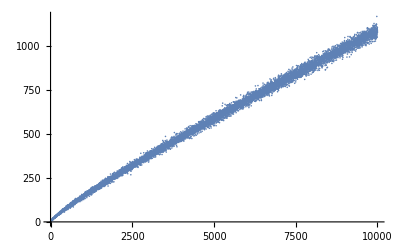

```mathematica
ListPlot@L
```

### Exercise Subsection

a. Create a function named PrimePositions[L_] which selects from L those elements in position 2, 3, 5, 7, 11,....  That is, return the elements in L that have a prime position in L.

```mathematica
PrimePositions[L_]:=L[[Cases[Range@Length@L,i_/;PrimeQ@i]]]
```

b. The function SpiralSteps defined in the next cell

```mathematica
SpiralSteps[n_]:=If[n==0,{π/2,π/2},Join[SpiralSteps[n-1],{π/2},Table[0,n],{π/2},Table[0,n]]]
```

```mathematica
SpiralSteps[4]
```

{π/2,π/2,π/2,0,π/2,0,π/2,0,0,π/2,0,0,π/2,0,0,0,π/2,0,0,0,π/2,0,0,0,0,π/2,0,0,0,0}

defines a sequence of steps that can be used to create a spiral using AnglePath:

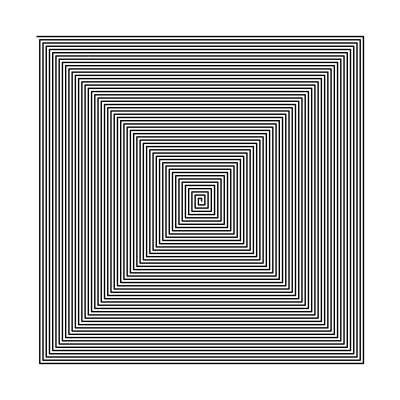

```mathematica
Graphics@Line@AnglePath@SpiralSteps@100
```

Use PrimePositions together with Graphics to place a Point at each coordinate in AnglePath@SpiralSteps@100 that is in a prime position.  The result is Ulam’s spiral (see https://en.wikipedia.org/wiki/Ulam_spiral ), which is interesting because so many points in the image lie on collinear diagonals.

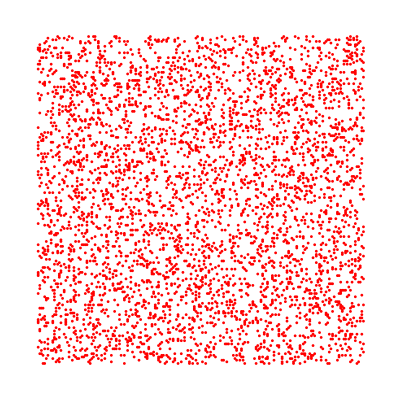
{-Graphics-,-Graphics-}

```mathematica
{Graphics[{Red,PointSize[.005],Point@PrimePositions@AnglePath@SpiralSteps@500,Black,Opacity[.0],Line@AnglePath@SpiralSteps@500}],
Graphics[{Red,PointSize[.005],Point@RandomSample[AnglePath@SpiralSteps@200,PrimePi@Length@SpiralSteps@200],Black,Opacity[.0],Line@AnglePath@SpiralSteps@200}]}
```

## Congruence equations

### Exercise Subsection

Equations (and systems of equations) can be solved working modulo m using the Modulus -> m option in Solve.  For example, solve the following equations working modulo 100, and then check that the answers are correct:

```mathematica
equation1=19x==1;
equation2={3 x+2y==4,2x+7y==6};
equation3={x^2+3 x y+y^2==1,2x^2-y==99};
equation4={{21,50,60,17,35},{29,40,9,42,34},{7,8,60,44,48},{97,6,38,9,90},{16,29,85,2,82}}.{a,b,c,d,e}=={1,2,3,4,5};
```

```mathematica
x/.First@Solve[equation1,Modulus->100]
```

79

```mathematica
Clear[a,b,c]
```

```mathematica
{3 x+2y,2x+7y}/.Solve[equation2,Modulus->100]
```

{{204,306}}

```mathematica
Solve[equation4,Modulus->100]
```

{{e→27,d→91,c→9,b→80,a→89}}

### Exercise Subsection

A multiplicative inverse to a modulo m is a solution to the equation a x == 1 modulo m.  Write a function MultInverse[a_,m_] that has input integers a and m and output {True, x} if x is the multiplicative inverse to a modulo m and {False} if no such x exists.

The multiplicative inverse to 20 working modulo 49 is equal to the following:

```mathematica
Solve[20 x==1,Modulus->49]
```

{{x→27}}

```mathematica
MultInverse[a_,m_]:=x/.First@Solve[a x==1,Modulus->m]
```

```mathematica
MultInverse[20,49]
```

27

### Exercise Subsection

A woman with a basket of eggs finds that if she removes either 2, 3, 4, 5, or 6 at a time from the basket, there is always one egg left over . If she removes 7 eggs at a time from the basket, there are no eggs left over . What is the minimum number of eggs in the basket?  (Look up and use the function ChineseRemainder to solve this exercise.)

### Exercise Subsection

The integer a between 0 and m-1 is a quadratic residue modulo m if there is at least one solution to the equation x^2 == a modulo m.  Write a function QuadraticResidue[m_] which produces a list of all quadratic residues modulo m.

```mathematica
QuadraticResidue[m_]:=Cases[If[Solve[x^2==#,Modulus->m]!={},#,-1]&/@Range[0,m-1],a_/;a!=-1]
```

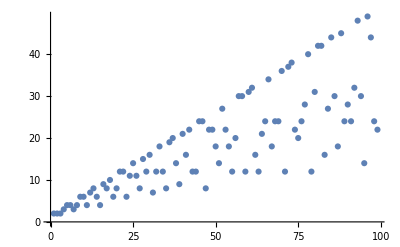

```mathematica
Table[QuadraticResidue[n]//Length,{n,2,100}]//ListPlot
```

## Number theoretic functions

### Exercise Subsection

EulerPhi is a function that has input a positive integer n and output equal to the number of positive integers smaller than n that are relatively prime to n.
a. Make a ListPlot of the first 1000 values of EulerPhi.

b. Find the least value of n such that EulerPhi gives the same output for n, n+1, and n+2.

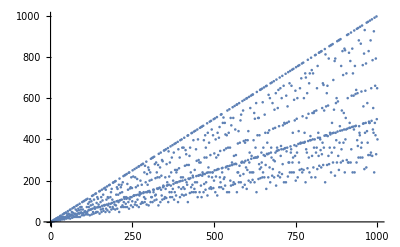

```mathematica
EulerPhi/@Range@1000//ListPlot
```

```mathematica
Cases[Table[{n,EulerPhi@n==EulerPhi[n+1]==EulerPhi[n+2]},{n,10000}],{a_,b_}/;b]
```

{{5186,True}}

```mathematica
EulerPhi[5186]
```

2592

```mathematica
EulerPhi[5188]
```

2592

### Exercise Subsection

a. The function PrimeOmega[n] gives the number of primes that divide n, counting multiplicities.  Create a list of length 20 such that element i on the list is the number of times an integer n between 1 and 10^5 has PrimeOmega[n] equal to i.  Then use ListPlot on this list to see the distribution of PrimeOmega[n] for values of n between 1 and 10^5.

b. Using the function

```mathematica
SpiralSteps[n_]:=If[n==0,{π/2,π/2},Join[SpiralSteps[n-1],{π/2},Table[0,n],{π/2},Table[0,n]]]
```

defined in a previous exercise, the next line defines a graphic that places a point with a radius that depends on PrimeOmega at each point along the spiral.  Admire the graphic!  That’s all you need to do: admire it!

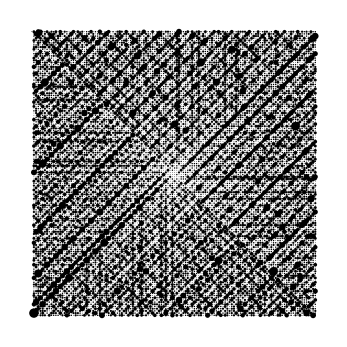

```mathematica
Graphics@Module[{steps=AnglePath@SpiralSteps@128},Table[{PointSize[0.0015*(PrimeOmega@i-1)],Point@steps[[i]]},{i,Length@steps}]]
```

### Exercise Subsection

The function Zeta[s] gives the Riemann zeta function at the complex number s.  This function is related to the distribution of prime numbers.  

a. Find the first 10 terms in the Series expansion of 1/Zeta[s] centered at s=5, using N to approximate the coefficients.  Then show this is very close to the series centered at s=5 for the function in the next cell.

```mathematica
Series[N@(1-2^-s) (1-3^-s) (1-5^-s) (1-7^-s) (1-11^-s) (1-13^-s) (1-17^-s) (1-19^-s) (1-23^-s) (1-29^-s),{s,5,10}]
```

0.964387+0.0265746 (s-5)-0.0103028 (s-5)^2+0.00280993 (s-5)^3-0.000616701 (s-5)^4+0.000117808 (s-5)^5-0.0000205238 (s-5)^6+3.32585×10^-6 (s-5)^7-4.95091×10^-7 (s-5)^8+6.2556×10^-8 (s-5)^9-4.41624×10^-9 (s-5)^10+O[s-5]^11

```mathematica
Series[N@1/Zeta[s],{s,5,10}]
```

0.964387+0.0265748 (s-5)-0.0103033 (s-5)^2+0.00281052 (s-5)^3-0.000617233 (s-5)^4+0.000118196 (s-5)^5-0.0000207606 (s-5)^6+3.45012×10^-6 (s-5)^7-5.52342×10^-7 (s-5)^8+8.60861×10^-8 (s-5)^9-1.31507×10^-8 (s-5)^10+O[s-5]^11

b. Simplify the infinite sum of terms of the form EulerPhi[n]/n^s as n ranges from 1 to Infinity to find an expression involving the Zeta function.

```mathematica
Sum[EulerPhi[n]/n^s,{n,1,Infinity}]
```

Zeta[-1+s]/Zeta[s]

### Exercise Subsection

Find at least 10 values of n such that EulerPhi[DivisiorSigma[1,n]] is equal to n.